## Importing the ^163 Lu data from CXX output

## Graphical representation for the excitation energies and contour plots for all the approaches used in novel formalism

```mathematica
approachA1=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitA1_cxx.dat"];
approachA2=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitA2_cxx.dat"];
approachB1=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitB1_cxx.dat"];
approachB2=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Data/Unified_Model/fitB2_cxx.dat"];
```

## Storing the fit parameters

```mathematica
paramsA1=approachA1[[1]];
paramsA2=approachA2[[1]];
paramsB1=approachB1[[1]];
paramsB2=approachB2[[1]];
```

## Storing the spins for each state (same across approaches)

```mathematica
spin1=Table[approachA1[[i,1]],{i,2,22}];
spin2=Table[approachA1[[i,1]],{i,23,39}];
spin3=Table[approachA1[[i,1]],{i,40,53}];
spin4=Table[approachA1[[i,1]],{i,54,63}];
```

## Storing the excitation energies for each approach

### APPROACH A1

```mathematica
tsd1ExpA1=Table[approachA1[[i,2]],{i,2,22}];
tsd1ThA1=Table[approachA1[[i,3]],{i,2,22}];
tsd2ExpA1=Table[approachA1[[i,2]],{i,23,39}];
tsd2ThA1=Table[approachA1[[i,3]],{i,23,39}];
tsd3ExpA1=Table[approachA1[[i,2]],{i,40,53}];
tsd3ThA1=Table[approachA1[[i,3]],{i,40,53}];
tsd4ExpA1=Table[approachA1[[i,2]],{i,54,63}];
tsd4ThA1=Table[approachA1[[i,3]],{i,54,63}];
```

### APPROACH A2

```mathematica
tsd1ExpA2=Table[approachA2[[i,2]],{i,2,22}];
tsd1ThA2=Table[approachA2[[i,3]],{i,2,22}];
tsd2ExpA2=Table[approachA2[[i,2]],{i,23,39}];
tsd2ThA2=Table[approachA2[[i,3]],{i,23,39}];
tsd3ExpA2=Table[approachA2[[i,2]],{i,40,53}];
tsd3ThA2=Table[approachA2[[i,3]],{i,40,53}];
tsd4ExpA2=Table[approachA2[[i,2]],{i,54,63}];
tsd4ThA2=Table[approachA2[[i,3]],{i,54,63}];
```

### APPROACH B1

```mathematica
tsd1ExpB1=Table[approachB1[[i,2]],{i,2,22}];
tsd1ThB1=Table[approachB1[[i,3]],{i,2,22}];
tsd2ExpB1=Table[approachB1[[i,2]],{i,23,39}];
tsd2ThB1=Table[approachB1[[i,3]],{i,23,39}];
tsd3ExpB1=Table[approachB1[[i,2]],{i,40,53}];
tsd3ThB1=Table[approachB1[[i,3]],{i,40,53}];
tsd4ExpB1=Table[approachB1[[i,2]],{i,54,63}];
tsd4ThB1=Table[approachB1[[i,3]],{i,54,63}];
```

### APPROACH B2

```mathematica
tsd1ExpB2=Table[approachB2[[i,2]],{i,2,22}];
tsd1ThB2=Table[approachB2[[i,3]],{i,2,22}];
tsd2ExpB2=Table[approachB2[[i,2]],{i,23,39}];
tsd2ThB2=Table[approachB2[[i,3]],{i,23,39}];
tsd3ExpB2=Table[approachB2[[i,2]],{i,40,53}];
tsd3ThB2=Table[approachB2[[i,3]],{i,40,53}];
tsd4ExpB2=Table[approachB2[[i,2]],{i,54,63}];
tsd4ThB2=Table[approachB2[[i,3]],{i,54,63}];
```

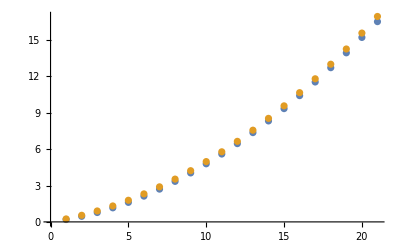

```mathematica
ListPlot[{tsd1ExpA1,tsd1ThA1}]
```